# Decision boundary Theory

```mathematica
fnew[dist_,fbase_, steps_, L_, r_, delta_] = (dist * L - dist  - r * Sum[((delta/(1+r))^t)*(fbase * L - fbase * t),{t, 1,steps}])/(L - 1 - r * Sum[((delta/(1+r))^t)*(L - t),{t, 1,steps}])
```

(-dist+dist L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

```mathematica
(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)
```

(-1+L-(delta fbase r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)/(-1+L-(delta r (-1+L-delta L-r+L r+(delta/(1+r))^steps-L (delta/(1+r))^steps+delta L (delta/(1+r))^steps+r (delta/(1+r))^steps-L r (delta/(1+r))^steps+(delta/(1+r))^steps steps-delta (delta/(1+r))^steps steps+r (delta/(1+r))^steps steps))/(-1+delta-r)^2)

30

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.25,1.24551,1.24155,1.23809,1.23507,1.23246,1.2302,1.22827,1.22661,1.2252,1.224,1.22299,1.22214,1.22143,1.22083,1.22034,1.21993,1.21959,1.21932,1.2191,1.21892,1.21878,1.21867,1.21858,1.21852,1.21847,1.21843,1.21841,1.2184,1.21839,1.21839},{1.5,1.49102,1.48311,1.47618,1.47015,1.46492,1.46041,1.45653,1.45322,1.4504,1.44801,1.44598,1.44428,1.44285,1.44166,1.44068,1.43986,1.43919,1.43864,1.4382,1.43784,1.43756,1.43734,1.43716,1.43703,1.43694,1.43687,1.43683,1.4368,1.43679,1.43679},{1.75,1.73653,1.72466,1.71427,1.70522,1.69738,1.69061,1.6848,1.67983,1.6756,1.67201,1.66898,1.66642,1.66428,1.6625,1.66101,1.65979,1.65878,1.65796,1.6573,1.65676,1.65634,1.656,1.65574,1.65555,1.65541,1.6553,1.65524,1.6552,1.65518,1.65518},{2.,1.98204,1.96621,1.95236,1.94029,1.92984,1.92082,1.91307,1.90644,1.9008,1.89601,1.89197,1.88856,1.88571,1.88333,1.88135,1.87972,1.87838,1.87728,1.87639,1.87568,1.87512,1.87467,1.87433,1.87407,1.87388,1.87374,1.87365,1.8736,1.87357,1.87357}}

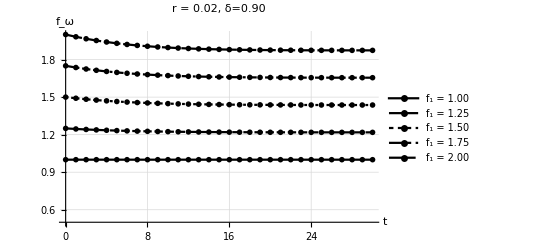

```mathematica
layers = 30
data = Table[Table[(factor -1 ) + fnew[1, factor,x,layers,0.02,0.9], {x,0,layers,1}], {factor, 1., 2., 0.25}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {0.5, 2.0}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.02, δ=0.90", PlotLegends->{"f_1 = 1.00", "f_1 = 1.25", "f_1 = 1.50", "f_1 = 1.75", "f_1 = 2.00"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
XCLAIM
```

```mathematica
buffer = (1 + 0.1706) * (1 + 0.7634) 
f1 = 1 * buffer
```

2.06424

2.06424

12

{2.06424,1.99264,1.93699,1.89387,1.86069,1.83545,1.81658,1.80282,1.79317,1.78681,1.78307,1.78143,1.78143}

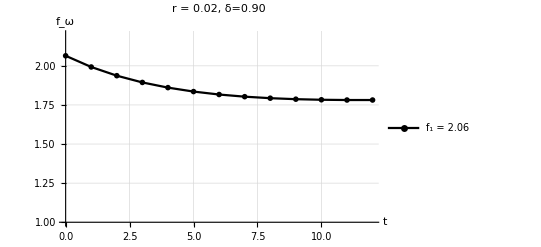

```mathematica
layers = 12
data = Table[fnew[f1,x,layers,0.02,0.9], {x,0,layers,1}]
ListLinePlot[data, PlotTheme->"Monochrome", PlotRange -> {1.0, 2.2}, AxesLabel->{"t", "f_ω"},PlotLabel-> "r = 0.02, δ=0.90", PlotLegends->{"f_1 = 2.06"}, GridLines->Automatic, DataRange->{0, layers}]
```

```mathematica
fomega = Last[data]
```

1.77861

```mathematica
1.8518166645938126
reduction = 1 - (fomega/f1)
```

1.85182

0.13837